```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["PhysicalConstants`"];
ch=PlanckConstant/(Joule Second);
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum={10094}];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
icycle=25;runi=1;
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
Print["Size of event list in Cycle: ",dimdata=Dimensions[data][[1]]];
```

General::obspkg: "PhysicalConstants`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: {10094}

Size of event list in Cycle: 451551

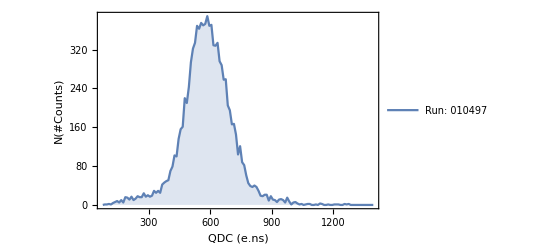

9858

```mathematica
ChNum=4;binw=10;
(*histdata=HistogramList[Select[data[[1;;dimdata,{3,7}]],#[[1]]==ChNum&][[;;,2]],{100,3000,binw}];*)
histdata=HistogramList[data[[Round[1(*dimdata/1.022318*)];;dimdata,6]],{70,1400,binw}];
ptdat=Table[{0,0},{k,1,Dimensions[histdata[[2]]][[1]]}];
For[i=1,i<=Dimensions[histdata[[2]]][[1]],i++,
ptdat[[i]][[1]]=1*(histdata[[1]][[i]]+((-histdata[[1]][[1]]+histdata[[1]][[2]])/2));
ptdat[[i]][[2]]=histdata[[2]][[i]];
];
ListLinePlot[{ptdat},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"QDC (e.ns)","N(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLegends->{"Run: 010497"},Filling->Axis,ImageSize->{1000}]
Total[histdata[[2]]]
```

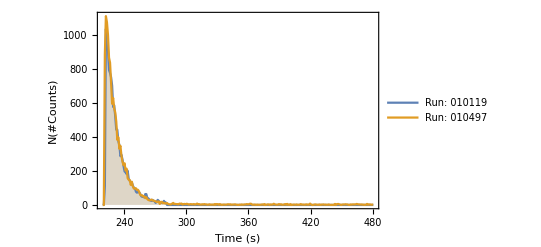

6594

```mathematica
histdata2=HistogramList[data[[Round[dimdata/1.022318];;dimdata,4]]/1000000000,{219,481,1}];
ptdat2=Table[{0,0},{k,1,Dimensions[histdata2[[2]]][[1]]}];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat2[[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2));
ptdat2[[i]][[2]]=2*histdata2[[2]][[i]];
];
ListLinePlot[{ptdat4,ptdat2},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Time (s)","N(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLegends->{"Run: 010119","Run: 010497"},Filling->Axis,ImageSize->{1000}]
Total[histdata2[[2]]]
```

```mathematica
Clear[histdata,histdata2]
```

```mathematica
ptdat[[1;;2]]
```

{{75,1},{85,0}}